```mathematica
RandomInteger[1]
```

1

```mathematica
length=10;n=length; LBern=RandomInteger[1,n]
```

{1,1,0,1,1,1,0,1,0,0}

```mathematica
LCoinToss=-1+2*LBern
```

{1,1,-1,1,1,1,-1,1,-1,-1}

```mathematica
LWalk=Accumulate[LCoinToss]
```

{1,2,1,2,3,4,3,4,3,2}

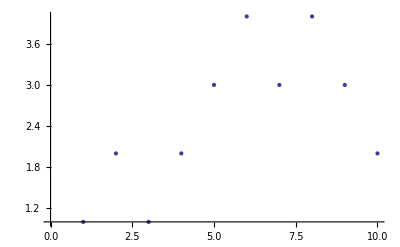

```mathematica
ListPlot[LWalk]
```

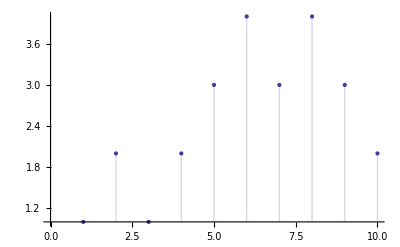

```mathematica
ListPlot[LWalk, Filling->Axis]
```

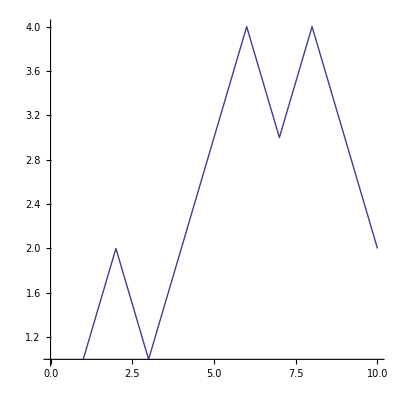

```mathematica
ListPlot[LWalk, AspectRatio -> 1, Joined -> True]
```

```mathematica
LWalk=Prepend[Accumulate[LCoinToss],0]
```

{0,1,2,1,2,3,4,3,4,3,2}

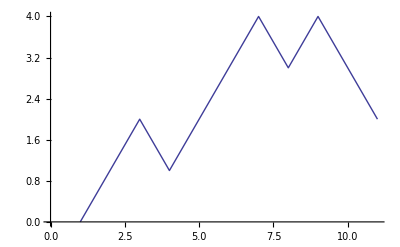

```mathematica
ListLinePlot[LWalk]
```

```mathematica
WalkToPlot[w_]:=Table[{i-1,w[[i]]}, {i,1,Length[w]}]
```

```mathematica
WalkToPlot[LWalk]
```

{{0,0},{1,1},{2,2},{3,1},{4,2},{5,3},{6,4},{7,3},{8,4},{9,3},{10,2}}

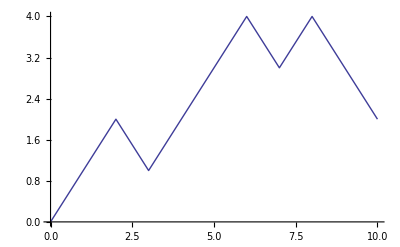

```mathematica
ListLinePlot[WalkToPlot[LWalk]]
```